```mathematica
littlewood[n_Integer,x_:x]:=1+Tuples[{1,-1},n]. x^Range[n]
```

```mathematica
littlewood[3]//Column//TraditionalForm
```

x^3+x^2+x+1
-x^3+x^2+x+1
x^3-x^2+x+1
-x^3-x^2+x+1
x^3+x^2-x+1
-x^3+x^2-x+1
x^3-x^2-x+1
-x^3-x^2-x+1

```mathematica
littlewoodRoots[n_]:= ComplexListPlot[x/. Solve[Times @@ littlewood[n]==0, x]]
```

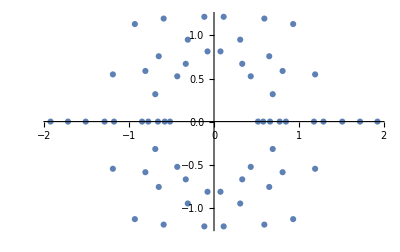

```mathematica
littlewoodRoots[4]
```

#### A fancier function with a slight increase in speed:

```mathematica
fastRootCalculate[n_Integer,x_:Unique[]]:=With[{
poly=1+Map[{1}~Join~#&,Tuples[{1,-1},n-1]]. #^Range[n]&,
solve=If[$VersionNumber<12.3,x/.NSolve@##&,NSolveValues],
mirror=If[n>3,Thread,Identity]@Join[#,-#]&,
map=If[n>5,ParallelMap,Map],
k=Floor[n/4]-$KernelCount},
If[k>0,LaunchKernels@k];
map[solve[#==0,x]&,poly@x]//mirror]
```

```mathematica
Block[{r,k=4-$KernelCount},If[k>0,LaunchKernels@k];
AbsoluteTiming[r=fastRootCalculate[10];]]
```

{0.428502,Null}

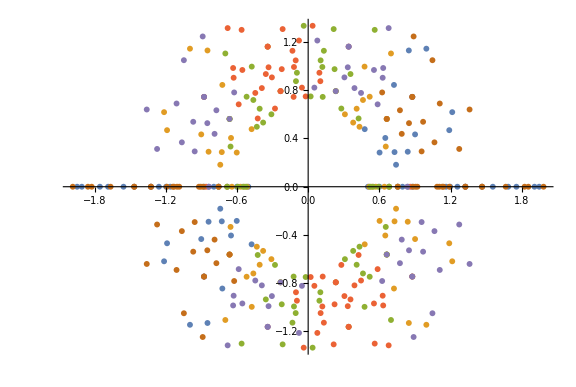

```mathematica
ComplexListPlot[fastRootCalculate[6],ImageSize->Large]
```

```mathematica
displayRoots[n_]:=With[{
p=fastRootCalculate[n],
c=Hue[#/n,1,1,If[n>12&&n<15,.3n-3.4,1]]&~Array~n,
s=AbsolutePointSize@If[n>15,1/(n-14),16-n],
r=PlotRange->4.1{#,#}2^-{1,3/2}&[{-1,1}],
l=PlotLabel->Style[Row@{"n = ",n},FontSize->(n+7)3],
w=ImageSize->(n+7)125},
If[n>5,
Graphics[Flatten@{s,{#1,Point@ReIm[#2]}&~MapThread~{c,p}},
w,l,r],
ComplexListPlot[p,PlotStyle->s,
AspectRatio->Tr@Ratios[Differences/@Last@r],w,l,r]]
]
```

```mathematica
Block[{r},AbsoluteTiming[r=fastRootCalculate@18;]]
```

{139.917,Null}

```mathematica
Block[{g=Table[Graphics[],18],t},
t=Table[{0,0},Length@g+2];
Do[
t[[i,1]]=First@AbsoluteTiming[g[[i]]=displayRoots[i];];
t[[i,2]]=First@AbsoluteTiming[Export[ToString@i<>".png",g[[i]]];],
{i,Length@g}];
t[[-2]]=AbsoluteTiming[g=MapThread[Magnify,{g,25/(7+Range@Length@g)}];];
t[[-1]]=AbsoluteTiming[Export["root.gif",g,"DisplayDurations"->3/2];];
Column@t]
```

{0.152367,1.77574}
{0.0354856,0.256212}
{0.0365752,0.319267}
{0.0407848,0.331847}
{0.0700865,0.37389}
{0.0411453,0.455968}
{0.0758049,0.500657}
{0.109103,0.567678}
{0.232459,0.69544}
{0.400258,0.935489}
{0.889953,1.30503}
{1.69287,2.08852}
{3.42427,3.20096}
{6.99652,5.39106}
{14.3788,10.7279}
{31.3342,21.8216}
{66.4252,44.7736}
{139.535,94.0885}
{0.0002375,Null}
{205.711,Null}